```mathematica
NotebookEvaluate["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/00_SplinePack-034.nb"]//Quiet;

Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/TP_ImProc_01-m101.wl"]//Quiet;

Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/TP_ImProc_01-m101.wl"]//Quiet;
```

```mathematica
Clear[e,f,F,G,h,M,n,P,p,Q,q,R,s,μ,σ]
```

```mathematica
{M,G,h}=Get[F="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20241123-01/Fig/TaskPlots/P-s/Speaking%20With%20Surgical%20Mask.dat"];
```

```mathematica
n =   Length[M]
μ = First/@M
σ =   Last/@M
OrderedQ[μ]
```

29

{-164.,-163.,-136.,-122.,-89.,-66.,-50.,-1.,2.,31.,78.,88.,114.,432.,447.,455.,473.,474.,486.,513.,559.,564.,586.,666.,776.,943.,947.,970.,1125.}

{273.,249.,279.,196.,291.,142.,107.,184.,413.,316.,93.,239.,267.,245.,189.,293.,83.,368.,220.,395.,162.,295.,610.,215.,531.,173.,475.,160.,161.}

True

```mathematica
Q = LogNormalDistribution[e,s];
startpar = FindDistributionParameters[Select[μ,Positive],Q];
p = N[Range[n]/(1+n)];
q = Quantile[Q,p];
f = μ-q;
f /= σ;
f = f.f;
f = FindMinimum[f,List@@@startpar];
Q = Q/.Last[f];
```

Measurement | TaskPlots
P-s
Speaking With Surgical Mask
n | 29
p-value (χ^2) | 0.323944
Distribution | LogNormalDistribution[5.62905,0.845043]
Mode | 136.313
Median | 278.397
Mean | 397.859
Quartiles | 157.445
278.397
492.267
StandardDeviation | 406.195

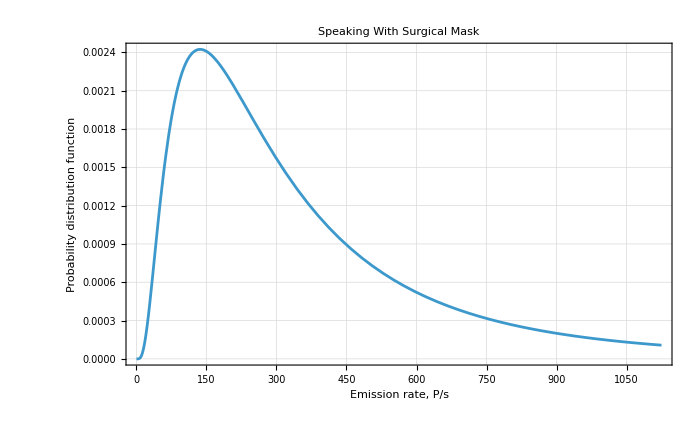

```mathematica
P = {Median,Mean,Quartiles,StandardDeviation};
P = Rule@@@Transpose[{ToString/@P,Map[#[Q]&,P]}];
PrependTo[P,"Mode"->("Median"^3/"Mean"^2)/.P];                                      (*    gilt nur für die LogNormalVerteilung    *)
PrependTo[P,"Distribution"->Q];
PrependTo[P,"p-value (χ^2)"->CDF[ChiSquareDistribution[n-2],First[f]]];
PrependTo[P,"n"->n];
PrependTo[P,"Measurement"->StringReplace[(taskname=Take[StringSplit[F,{".","/"}],{-4,-2}]),"%20"->" "]];
TableForm[List@@@P]

Plot[
PDF[Q,x],{x,0,Last[μ]},
Frame->True,
FrameLabel->{Last[FrameLabel/.Rest[List@@G]],"Probability distribution function"},
GridLines->Automatic,
ImageSize->700,
LabelStyle->{
FontColor->GrayLevel[0],
FontFamily->"Lucida Sans Unicode",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->14},
PlotLabel->Last["Measurement"/.P],
PlotRange->All]
```

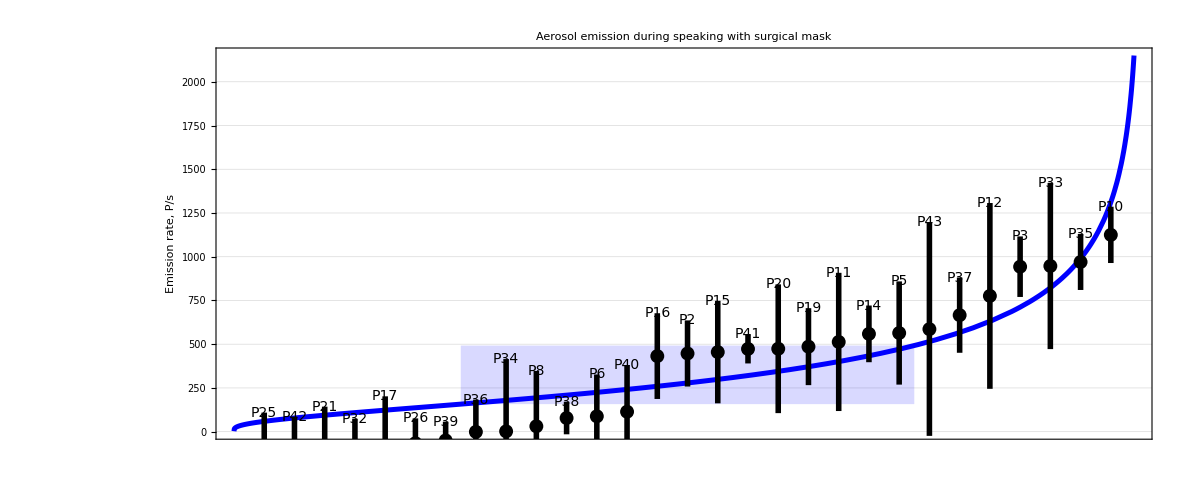

```mathematica
Clear[f];
f[k_] := Quantile[Q,k/(1+n)];
L = Plot[f[x],{x,0,n+1},DisplayFunction->Identity,PlotRange->(PlotRange/.Rest[List@@G])];
L = Extract[L,Most[First[Position[L,Line]]]];
R = Transpose[{(1+n)*{1,3}/4.,("Quartiles"/.P)[[{1,3}]]}];
h = ReplacePart[G,
Prepend[G[[1]],
{Blue,
{Opacity[0.15],Rectangle@@R},
{Thickness[0.003],L}}
],1];
h = h/.{
"Arial"->"Lucida Sans Unicode",
(FontSize -> 16)->(FontSize -> 14)}
```

```mathematica
Export[StringJoin[NotebookDirectory[],"\\output directory\\","Speaking With Surgical Mask","_lognormal.svg"],h]
```

C:\Users\mona_\Downloads\upload aerosol study 2020\\output directory\Speaking With Surgical Mask_lognormal.svg

```mathematica
(*

ENDE

*)
```

```mathematica
Clear[L,k,n]
```

```mathematica
L = p^k*(1-p)^(1+n-k)
```

(1-p)^(1-k+n) p^k

```mathematica
Solve[D[Log[L],p]/L==0,p]
```

{{p→ConditionalExpression[0, Re[k]<-1]},{p→ConditionalExpression[1, Re[n]<-2+Re[k]]},{p→k/(1+n)}}